```mathematica
SetOptions[Plot,Frame->True];
```

## density matrix |ψ(α,ϕ)> = Sin[α]|HH> + exp(iϕ)Cos[α] |VV> ρ = |ψ><ψ|

```mathematica
(* Basis: {HH,HV,VH,VV} *)
(* 
|α> = Sin[α]|H> + Cos[α]|V>,
|β> = Sin[β]|H> + Cos[β]|V>
*)
αβ[α_,β_]:= {Sin[α]*Sin[β],Sin[α]*Cos[β],Cos[α]*Sin[β],Cos[α]*Cos[β]} 
(* density matrix of a quantum state Sin[α] |HH> + Cos[α]Exp[I*ϕ] |VV> *)
dm[ϕ_,α_]:={{Sin[α]^2,0,0,Sin[α]*Cos[α]*Exp[-I*ϕ]},{0,0,0,0},{0,0,0,0},{Sin[α]*Cos[α]*Exp[I*ϕ],0,0,Cos[α]^2}};
dm[ϕ_]:= dm[ϕ,π/4];
(* dm[ϕ_]:=1/2{{1,0,0,Exp[-I*ϕ]},{0,0,0,0},{0,0,0,0},{Exp[I*ϕ],0,0,1}}; *)
dm[ϕ,α] // MatrixForm
dm[ϕ] //MatrixForm
```

(Sin[α]^2 | 0 | 0 | ⅇ^(-ⅈ ϕ) Cos[α] Sin[α]
0 | 0 | 0 | 0
0 | 0 | 0 | 0
ⅇ^(ⅈ ϕ) Cos[α] Sin[α] | 0 | 0 | Cos[α]^2)

(1/2 | 0 | 0 | ⅇ^(-ⅈ ϕ)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
ⅇ^(ⅈ ϕ)/2 | 0 | 0 | 1/2)

```mathematica
(* detection probability: density matrix ρ, measurement angles α and β *)
PDet[ρ_,α_,β_]:= αβ[α,β].ρ.αβ[α,β];
(* expectation value *)
EValue[ρ_,α_,β_]:= αβ[α,β].ρ.αβ[α,β] + αβ[α+π/2,β+π/2].ρ.αβ[α+π/2,β+π/2] -αβ[α+π/2,β].ρ.αβ[α+π/2,β]-αβ[α,β+π/2].ρ.αβ[α,β+π/2];
```

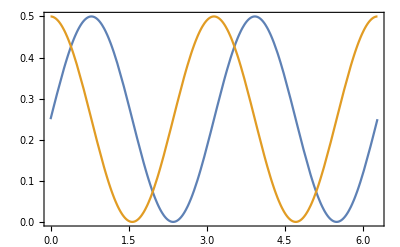

```mathematica
Plot[{PDet[dm[0],π/4,β],PDet[dm[0],0,β]},{β,0,2π}]
```

## Random Phase Example phase between 170 degrees and 190 degrees

```mathematica
Δphi = 10; (* degrees *)
ranphdm = 1/1000*Sum[dm[RandomReal[{(180-Δphi)/180*π,(180+Δphi)/180*π}]],{i,1,1000}]
```

{{1/2,0,0,-0.497407+0.00243758 ⅈ},{0,0,0,0},{0,0,0,0},{-0.497407-0.00243758 ⅈ,0,0,1/2}}

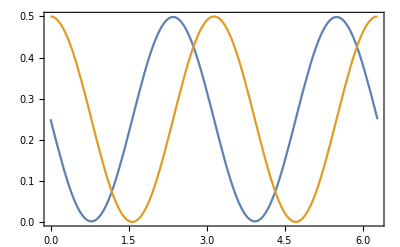

```mathematica
Plot[{PDet[ranphdm,π/4,β],PDet[ranphdm,0,β]},{β,0,2π}]
```

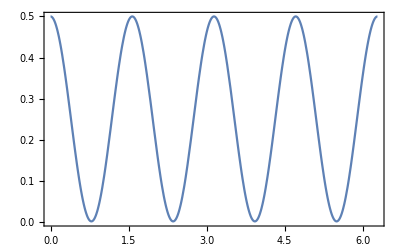

```mathematica
(* one polarizer *)
Plot[{PDet[ranphdm,β,β]},{β,0,2π}]
```

## Random Phase Example phase between 150 degrees and 210 degrees

```mathematica
Δphi = 30; (* degrees *)
ranphdm = 1/1000*Sum[dm[RandomReal[{(180-Δphi)/180*π,(180+Δphi)/180*π}]],{i,1,1000}]
```

{{1/2,0,0,-0.477378-0.000523748 ⅈ},{0,0,0,0},{0,0,0,0},{-0.477378+0.000523748 ⅈ,0,0,1/2}}

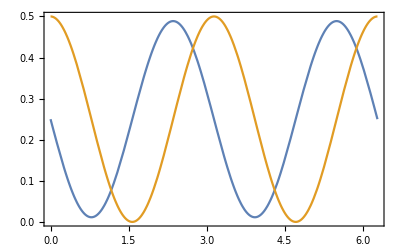

```mathematica
Plot[{PDet[ranphdm,π/4,β],PDet[ranphdm,0,β]},{β,0,2π}]
```

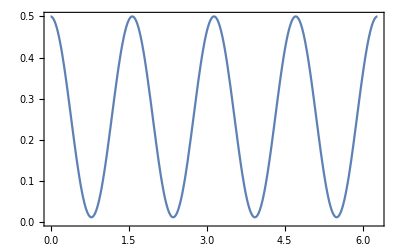

```mathematica
(* one polarizer *)
Plot[{PDet[ranphdm,β,β],PlotRange->{All,{0,.5}}},{β,0,2π}]
```

## Random Phase Example phase between -180 degrees and +180 degrees

```mathematica
Δphi = 180; (* degrees *)
ranphdm = 1/1000*Sum[dm[RandomReal[{(180-Δphi)/180*π,(180+Δphi)/180*π}]],{i,1,1000}]
```

{{1/2,0,0,-0.000496243-0.0144421 ⅈ},{0,0,0,0},{0,0,0,0},{-0.000496243+0.0144421 ⅈ,0,0,1/2}}

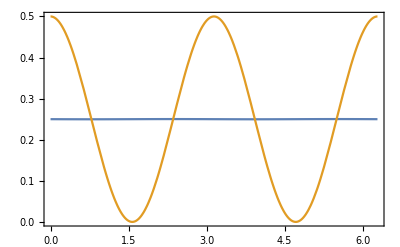

```mathematica
Plot[{PDet[ranphdm,π/4,β],PDet[ranphdm,0,β]},{β,0,2π}]
```

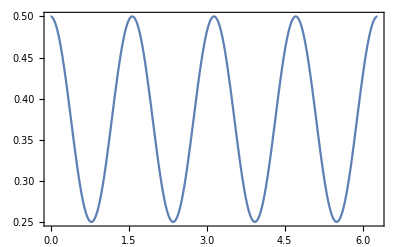

```mathematica
(* one polarizer *)
Plot[{PDet[ranphdm,β,β]},{β,0,2π}]
```